```mathematica
(*Mathematica
(*Gell-Mann SU(3)*)*)
```

```mathematica
s[1]={{0,1,0},{1,0,0},{0,0,0}};
```

```mathematica
s[2]={{0,-I,0},{I,0,0},{0,0,0}};
```

```mathematica
s[3]={{1,0,0},{0,-1,0},{0,0,0}};
```

```mathematica
s[4]={{0,0,1},{0,0,0},{1,0,0}};
```

```mathematica
s[5]={{0,0,-I},{0,0,0},{I,0,0}};
```

```mathematica
s[6]={{0,0,0},{0,0,1},{0,1,0}};
```

```mathematica
s[7]={{0,0,0},{0,0,-I},{0,I,0}};
```

```mathematica
s[8]={{1,0,0},{0,1,0},{0,0,-2}}/Sqrt[3];
```

```mathematica
s[9]={{1,0,0},{0,1,0},{0,0,1}};
```

```mathematica
(*Cycle:Octagon*)
```

```mathematica
Apply[Dot,Table[s[i],{i,8}]]
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
Table[Det[s[i]],{i,8}]
Table[Tr[s[i]],{i,8}]
```

{0,0,0,0,0,0,0,-2/(3 √3)}

{0,0,0,0,0,0,0,0}

```mathematica
(*Casimir invariant*)
ci=Sum[s[i].s[i],{i,8}]
```

{{16/3,0,0},{0,16/3,0},{0,0,16/3}}

```mathematica
(*Lehmer Salem*)
```

```mathematica
u=z/.NSolve[-1-2 z-2 z^2-2 z^3+2 z^5+2 z^6+2 z^7+z^8==0,z]
```

{-1.,-1.,-1.,0.-1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.+1. ⅈ,1.}

```mathematica
p[z_]=-1-2 z-2 z^2-2 z^3+2 z^5+2 z^6+2 z^7+z^8
```

-1-2 z-2 z^2-2 z^3+2 z^5+2 z^6+2 z^7+z^8

```mathematica
r[i_]:=z/.NSolve[p[z]==0,z][[i]]
```

```mathematica
w=Table[r[i],{i,8}]
```

{-1.,-1.,-1.,0.-1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.+1. ⅈ,1.}

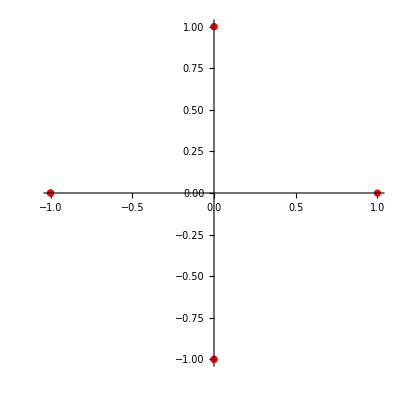

```mathematica
ComplexListPlot[w,PlotStyle->Red]
```

```mathematica
(*SL(3,c) matrix*)
```

```mathematica
m=(s[9]+Sum[s[i]*r[i],{i,8}])/2.388602512436506^(1/3)
```

{{0.431908+0. ⅈ,-0.748087+0.748087 ⅈ,-0.748087-0.748087 ⅈ},{-0.748087-0.748087 ⅈ,1.92808+0. ⅈ,0.748087+0.748087 ⅈ},{0.748087-0.748087 ⅈ,-0.748087+0.748087 ⅈ,-0.115729+0. ⅈ}}

```mathematica
dt=Det[m]//Chop
```

1.

```mathematica
Tr[m]
```

2.24426+0. ⅈ

```mathematica
msl=(s[9]+Sum[s[i]*(z-r[i]),{i,8}])/2.388602512436506^(1/3)
```

{{0.748087 (2.+(-1.+z)/(√3)+z),0.748087 (1.+z-ⅈ (1.+z)),0.748087 ((0.+1. ⅈ)+z-ⅈ ((0.+1. ⅈ)+z))},{0.748087 (1.+z+ⅈ (1.+z)),0.748087 (0.+(-1.+z)/(√3)-z),0.748087 ((0.-1. ⅈ)+z-ⅈ ((0.-1. ⅈ)+z))},{0.748087 ((0.+1. ⅈ)+z+ⅈ ((0.+1. ⅈ)+z)),0.748087 ((0.-1. ⅈ)+z+ⅈ ((0.-1. ⅈ)+z)),0.748087 (1-(2 (-1.+z))/(√3))}}

```mathematica
f[z_]=ExpandAll[CharacteristicPolynomial[msl,z]/(5.473971846853062)]//Chop
```

-0.0297207-(0.483332-0.611848 ⅈ) z+(1.04288+0.611848 ⅈ) z^2+1. z^3

```mathematica
v=z/.NSolve[f[z]==0,z]
```

{-1.34068-0.128503 ⅈ,-0.0259847-0.0298885 ⅈ,0.323784-0.453456 ⅈ}

```mathematica
max=Max[Norm/@v]+1.0
```

2.34682

```mathematica
ga=ComplexPlot[f[z],{z,-max-I*(max-0.5),max+I*(max-0.5)},ColorFunction->"CyclicReImLogAbs",ImageSize->2000,PlotPoints->100];
```

```mathematica
gb=ComplexPlot3D[f[z],{z,-max-I*(max-0.5),max+I*(max-0.5)},ColorFunction->"CyclicReImLogAbs",ImageSize->2000,PlotPoints->100,ViewPoint->Above];
```

```mathematica
g0=JuliaSetPlot[f[x]*1.0615,x,ColorFunction->Hue,ImageSize->2000,AspectRatio->1,ImageResolution->2000,PerformanceGoal->"Quality",Frame->False,Axes->False,PlotRange->All];
g03=ListPlot[JuliaSetPoints[f[x]*1.0615,x],ImageSize->2000,PlotStyle->{PointSize[0.001]},ColorFunction->Hue,PlotRange->All,AspectRatio->1,Background->Black];
Export["Julia_SU3_Square_Polynomial_scale_1p0615_grid.jpg",GraphicsGrid[{{ga,gb}, 
 {g0,g03}},ImageSize->{4000,4000}]]
```

Julia_SU3_Square_Polynomial_scale_1p0615_grid.jpg

```mathematica
Clear[g1,g2]
```

#### 3D and plane Mandelbrots/ Julias

```mathematica
(*Julia with SQRT(x^2+y^2) limited measure*)
(*by R. L. BAGULA 28 Sept 20026© *)
numberOfz2ToEscape[z_] := Block[
	{escapeCount, nz = N[z],nzold=0},
	For[
		escapeCount = 0,
		(Sqrt[Re[nz]^2+Im[nz]^2] < 32) && (escapeCount < 512) && (Abs[nz-nzold]>.5*10^(-3)),
		nzold=nz;
		nz=f[nz]*1.0615;
		
    
		++escapeCount
	];
	escapeCount*If[(Abs[nz-nzold]>10^(-3)),Abs[ArcTan[nz]+I*ArcTan[nz]*Tan[1]-Arg[z]],Abs[Arg[nz]-Arg[nz]^3/3]]
]
```

```mathematica
FractalPureM[{{ReMin_, ReMax_, ReSteps_},
			 {ImMin_, ImMax_, ImSteps_}}] :=
		ParallelTable[
			numberOfz2ToEscape[x + y I],
			{y, ImMin, ImMax, (ImMax - ImMin)/ImSteps},
			{x, ReMin, ReMax, (ReMax - ReMin)/ReSteps}
		
	]
```

```mathematica
arraym=FractalPureM[{{-max+0.0001,max-0.75,1000},{-max+0.25,max-0.75,1000}}];
```

```mathematica
g1=ListPlot3D[Abs[Log[1/Max[arraym]+arraym]], Mesh -> False,AspectRatio -> Automatic,Boxed->False, Axes->False,ColorFunction→"Rainbow",Background→Black,ViewPoint→Above,ImageSize->{2000,2000}];
```

```mathematica
Export["j_1000_SU3_Square_Polynomial_In_Out_monitor_g1.jpg",g1]
```

j_1000_SU3_Square_Polynomial_In_Out_monitor_g1.jpg

```mathematica
g1a=ListPlot3D[Log[Abs[1/Max[arraym]+arraym-512/(arraym+Max[arraym])]], Mesh -> False,AspectRatio -> Automatic,Boxed->False, Axes->False,ColorFunction->Hue,Background->Black,ViewPoint->Above,ImageSize->{2000,2000}];
```

$Aborted

```mathematica
Export["j_1000_SU3_Square_Polynomial_In_Out_monitor_g1a.jpg",g1a]
```

```mathematica
g2=ListDensityPlot[Log[Abs[1/Max[arraym]+arraym-512/(arraym+Max[arraym])]],
                          Mesh -> False,
		                  AspectRatio -> Automatic,
		                ColorFunction-> (Hue[1.75*#]&),ImageSize->{2000,2000},Frame->False];
```

```mathematica
Export["j_1000_SU3_Square_Polynomial_In_Out_monitor_g2.jpg",g2]
```

```mathematica
g2a=ListDensityPlot[Log[Abs[1/Max[arraym]+arraym-512/(arraym+Max[arraym])]],
                          Mesh -> False,
		                  AspectRatio -> Automatic,
		                ColorFunction-> "Pastel",ImageSize->{2000,2000},Frame->False];
```

```mathematica
Export["j_1000_SU3_Square_Polynomial_In_Out_monitor_g2.jpg",g2]
```

```mathematica
colortab=Sort[Join[Flatten[Delete[Sort[Union[Table[Delete[Sort[Union[Flatten[Table[If[i+j+k==n,{(1)^2,(1-j)^2,(1-k)^2},{}],{i,0,1,1/10},{j,0,1,1/10},{k,0,1,1/10}],2]]],1],{n,0,1,1/30}]]],1],1],{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}},{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/2,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/1.5,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/3]];
```

```mathematica
Length[%]
```

542

```mathematica
cf[l_]:=Block[{niv,rgb},niv=If[l<1/542,1,Ceiling[542*l]];
rgb=colortab[[niv]];
RGBColor[rgb[[1]],rgb[[2]],rgb[[3]]]];
```

```mathematica
g3=ListDensityPlot[Abs[Log[1/Max[arraym]+arraym]], Mesh -> False, AspectRatio -> Automatic, ColorFunction->cf,ImageSize->{2000,2000},Frame->False];
```

```mathematica
Export["j_1000_SU3_Square_Polynomial_In_Out_monitor_g3.jpg",g3]
```

```mathematica
Export["j_1000_SU3_Square_Polynomial_In_Out_monitor_grid.jpg",GraphicsGrid[{{g0,g03,g2a},{ga,gb,g2}, 
 {g3,g1,g1a}},ImageSize->{6000,6000}]]
```

```mathematica
(*end*)
```